Autor: Imię i nazwisko

# Metody numeryczne

## (kierunek Informatyka)

## Projekt 8

Metoda Eulera

Napisać procedurę realizującą algorytm metody Eulera (argumenty:  f, x_0, y_0, b, n).

a) Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=(y(x))/x^2      dla x∈[1,10],
y(1)=2.

Obliczenia wykonać dla 40 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązanie przybliżone.
Wykreślić także błędy uzyskanego rozwiązania przybliżonego.

## Rozwiązanie

### Program

```mathematica
Clear[euler];
euler[f_,x0_,y0_,b_,n_]:=Module[{xo=x0,yo=y0,h,no,print,i,xn1},
h=(b-xo)/n;
no=Table[yo,n+1];
xn1=Table[xo,n+1];
print=Table[{xo,yo},n+1];
For [i=1,i≤ n,++i,
no[[i+1]]=no[[i]]+h*f[xn1[[i]],no[[i]]];
xn1[[i+1]]=xn1[[i]]+h;
print[[i+1]]={xn1[[i+1]],no[[i+1]]}
];

Return[print];]
```

### Zadanie a)

```mathematica
Clear[f,xo,yo,b,n,dokladnie,blad];
xo=1;
yo=2;
f[x_,y_]:=y/x^2;
b=10;
n=40;
(*obliczanie rozwiazania przyblizonego *)
przyblizenie=euler[f,xo,yo,b,n];
(* obliczanie dokladnego rozwiazania *)
dokladnie=DSolve[{y'[x]==y[x]/x^2,y[1]==2},y[x],x];
blad=Table[{1,0},40];
For[i=1,i≤40,++i,blad⟦i⟧={przyblizenie⟦i⟧⟦1⟧,Abs[przyblizenie⟦i⟧⟦2⟧-dokladnie⟦1,1,2⟧/.{x->przyblizenie⟦i⟧⟦1⟧}]}];
```

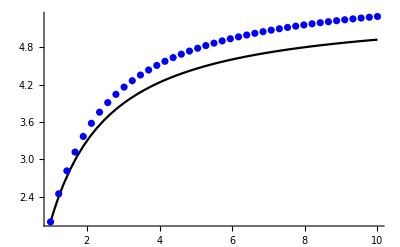

```mathematica
w1=Plot[dokladnie⟦1,1,2⟧,{x,1,10},PlotStyle->Black,AxesOrigin->{0,0}];
w2=ListPlot[przyblizenie,PlotStyle->Blue];
w3=ListPlot[blad,PlotStyle->Green];
Show[w1,w2,PlotRange->Automatic]
```

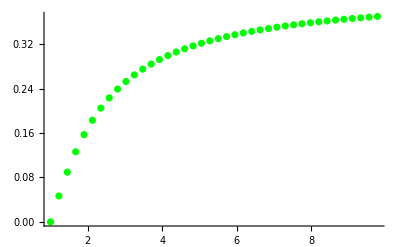

```mathematica
Show[w3,PlotRange->Automatic]
```